```mathematica
nBimport=Import["/Users/gpatenotte/Downloads/noB100000.csv"];
wBimport=Import["/Users/gpatenotte/Downloads/wB100000.csv"];
import//Dimensions
```

{1334,8}

```mathematica
dataHeaders=import[[1]]
```

{Time,Commanded Position,Input 2,Actual Motor Position,Amplifier Temperature,Actual Current,Hall Sensor State,}

```mathematica
nBdata=nBimport[[2;;]]ᵀ;
wBdata=wBimport[[2;;]]ᵀ;
```

```mathematica
{nBtime,nBgoalPosition,nBinput, nBactualPosition,nBtemperature,nBcurrent, nBsensor}=nBdata[[1;;7]];
{wBtime,wBgoalPosition,wBinput, wBactualPosition,wBtemperature,wBcurrent, wBsensor}=wBdata[[1;;7]];
```

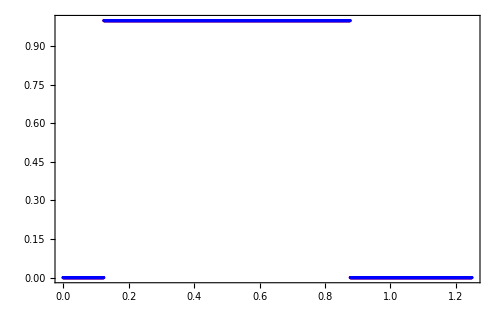

```mathematica
ListPlot[{Transpose@{time,wBinput},Transpose@{time,nBinput}},PlotStyle->{Red,Blue}]
```

```mathematica
nBtrigIndex=Flatten[Position[Differences[nBinput],#]&/@{-1,1}] (*in order of falling edge, then rising edge*)
wBtrigIndex=Flatten[Position[Differences[wBinput],#]&/@{-1,1}]
```

{936,133}

{936,133}

```mathematica
Max[nBgoalPosition]/14222.222-0.1
```

6.93125

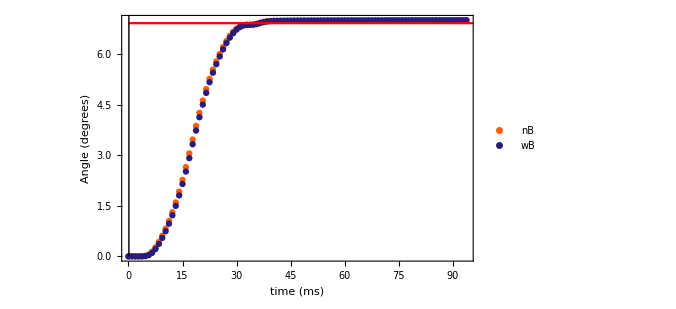

```mathematica
l1=Show[ListPlot[{(Transpose@{1000(nBtime-nBtime[[nBtrigIndex[[1]]]]),nBactualPosition/14222.222})[[nBtrigIndex[[1]]-0;;nBtrigIndex[[1]]+100]],(Transpose@{1000(wBtime-wBtime[[wBtrigIndex[[1]]]]),wBactualPosition/14222.222})[[wBtrigIndex[[1]]-0;;wBtrigIndex[[1]]+100]]},Epilog->Line[{{time[[trigIndex[[1]]]],0},{time[[trigIndex[[1]]]],Max[nBgoalPosition]}}],FrameLabel->{"time (ms)","Angle (degrees)"},PlotStyle->{ColorData[3][2],ColorData[3][7]},PlotLegends->{"nB","wB"}],Plot[Max[nBgoalPosition]/14222.222-0.1,{x,0,1000},PlotStyle->Red]]
```

```mathematica
0.1*14222.222
```

1422.22

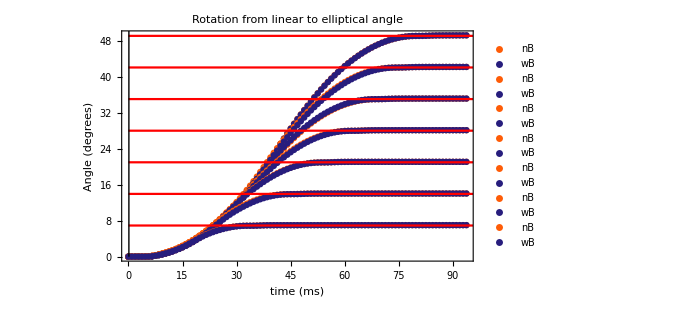

```mathematica
Show[l7,l6,l5,l4,l3,l2,l1,PlotLabel->"Rotation from linear to elliptical angle"]
```